```mathematica
Solve[{μ==α/(α+β), σ2==(α β)/((α+β)^2(α+β+1))},{β,α}]
```

{{β→((-1+μ) (-μ+μ^2+σ2))/σ2,α→(μ^2-μ^3-μ σ2)/σ2}}

```mathematica
a=α/4;
b=0;
c=α/16;
```

```mathematica
I2=Integrate[-y/(a*y^2+c),{y,0,x},Assumptions->{(α|x|y)∈Reals,α>0}]
```

ConditionalExpression[-(2 Log[1+4 x^2])/α,x>0]

```mathematica
Exp[(-4 ArcTan[2 x]+2 Log[1+4 x^2])/α]
```

ⅇ^((-4 ArcTan[2 x]+2 Log[1+4 x^2])/α)

```mathematica
Manipulate[Plot[ⅇ^((-4 ArcTan[2 x]+2 Log[1+4 x^2])/α),{x,-1,1}],{α,0.1,10}]
```

```mathematica
m=Exp[(4 ArcTan[2 x])/α]((1+4 x^2)^(-2/α))/(a*y^2+c)
```

(ⅇ^((4 ArcTan[2 x])/α) (1+4 x^2)^(-2/α))/(α/16+(y^2 α)/4)

```mathematica
Integrate[v/((α *v^2)/4+ α/16),v]
```

```mathematica
TeXForm[v/((α *v^2)/4+ α/16)]
```

\frac{v}{\frac{\alpha }{16}+\frac{\alpha  v^2}{4}}

```mathematica
z=Exp[(2 Log[1+4 v^2])/α]
```

(1+4 v^2)^(2/α)

```mathematica
TeXForm[(1+4 v^2)^(2/α)]
```

\left(4 v^2+1\right)^{2/\alpha }

```mathematica
m=1/((1+4 v^2)^(2/α)*((α *v^2)/4+ α/16))
```

((1+4 v^2)^(-2/α))/(α/16+(v^2 α)/4)

```mathematica
Simplify[m]
```

(16 (1+4 v^2)^(-(2+α)/α))/α

```mathematica
p=(1+4 v^2)^(-(2+α)/α)
```

(1+4 v^2)^(-(2+α)/α)

```mathematica
Integrate[(1+4 v^2)^(2/α),{v,0,Infinity}, Assumptions->{α>0}]
```

```mathematica
Integrate[(1+4 v^2)^(2/α),{v,0,21}, Assumptions->{α>0}]
```

21 Hypergeometric2F1[1/2,-2/α,3/2,-1764]

```mathematica
Integrate[(1+4 v^2)^(2/α),v]
```

```mathematica
v Hypergeometric2F1[1/2,-2/α,3/2,-4 v^2]Assumptions->{(α|x|y)∈Reals
```

```mathematica
v Hypergeometric2F1[1/2,-2/α,3/2,-4 v^2]/.{v-> -Infinity}
```

-∞ Hypergeometric2F1[1/2,-2/α,3/2,-∞]

```mathematica
∞ Hypergeometric2F1[1/2,-2/α,3/2,-∞]
```

∞ Hypergeometric2F1[1/2,-2/α,3/2,-∞]

```mathematica
(√π Gamma[-(4+α)/(2 α)])/(4 Gamma[-2/α])/.{α -> -100}
```

(√π Gamma[-12/25])/(4 Gamma[1/50])

```mathematica
N[(√π Gamma[-12/25])/(4 Gamma[1/50])]
```

-0.0318504

```mathematica
N[(√π Gamma[-13/25])/(4 Gamma[-1/50])]
```

0.0310779

```mathematica
TeXForm[p]
```

\left(4 v^2+1\right)^{-\frac{\alpha +2}{\alpha }}

```mathematica
Integrate[p,v]
```

v Hypergeometric2F1[1/2,(2+α)/α,3/2,-4 v^2]

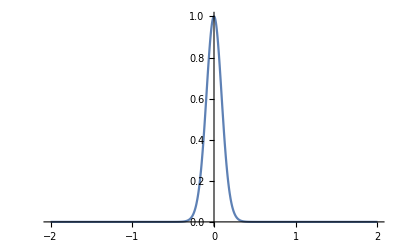

```mathematica
p2=Plot[p/.{α -> 0.15}, {v,-2,2},PlotRange-> {0,1}]
```

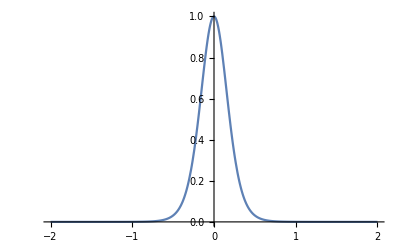

```mathematica
p3=Plot[p/.{α -> 0.5}, {v,-2,2},PlotRange-> {0,1}]
```

```mathematica
p
```

(1+4 v^2)^(-(2+α)/α)

```mathematica
M=2*Integrate[p,{v,0, Infinity}, Assumptions->{α>0}]
```

(√π Gamma[1/2+2/α])/(2 Gamma[(2+α)/α])

```mathematica
TeXForm[M]
```

\frac{\sqrt{\pi } \Gamma \left(\frac{1}{2}+\frac{2}{\alpha }\right)}{2 \Gamma \left(\frac{\alpha +2}{\alpha }\right)}

```mathematica
Integrate[p/M,{v,-Infinity, Infinity}, Assumptions->{α>0}]
```

1

```mathematica
Integrate[v*p/M,{v,-Infinity, Infinity}, Assumptions->{α>0}]
```

0

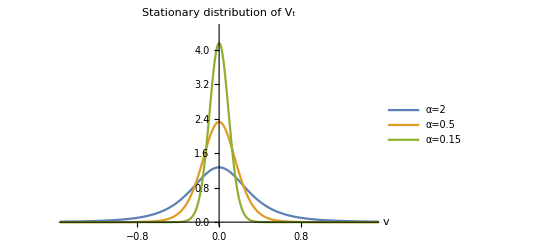

```mathematica
p4=Plot[{(p/M)/.{α -> 2}, (p/M)/.{α -> 0.5},(p/M)/.{α -> 0.15}}, {v,-5,5},PlotRange-> {{-1.5,1.5},{0,4.5}},PlotLegends->LineLegend[{"α=2","α=0.5","α=0.15 "}],PlotLabel->HoldForm[Stationary distribution of Subscript[V, t] ],AxesLabel->{HoldForm[v],None}]
```

```mathematica
Export["invarient_Vt.pdf",p4]
```

invarient_Vt.pdf

```mathematica
p/M
```

```mathematica
k=(2 (1+4 v^2)^(-(2+α)/α) Gamma[(2+α)/α])/(√π Gamma[1/2+2/α])/.{α -> 2, v-> v+500}
```

4/(π (1+4 (500+v)^2)^2)

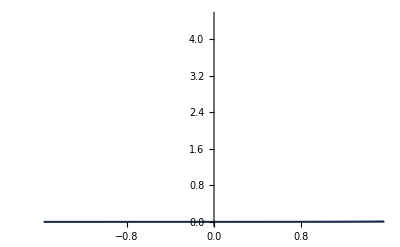

```mathematica
Plot[4/(π (1+4 (v-3)^2)^2),{v,-5,5},PlotRange-> {{-1.5,1.5},{0,4.5}}]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["invarient_Vt.pdf"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["invarient_Vt.pdf"]]]
```

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,5},PlotLegends->LineLegend[{Red,Green,Blue},Automatic]]
```

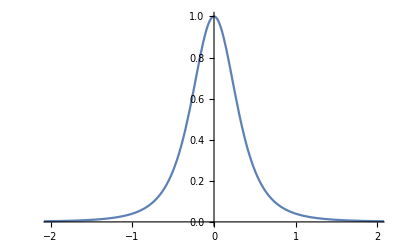
Show[-Graphics-,-Graphics-,-Graphics-,AxesLabel→{v,None},PlotLabel→Stationary distribution of V_t (α=0.15),LabelStyle→{GrayLevel[0]},]

```mathematica
Show[p2,p3,p4,AxesLabel->{HoldForm[v],None},PlotLabel->HoldForm[Stationary distribution of Subscript[V, t] (α=0.15)],LabelStyle->{GrayLevel[0]},LineLegend[{Red,Green,Blue},{"red","green","blue"}]]
```

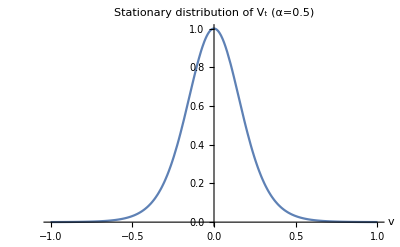

```mathematica
Show[%78,AxesLabel->{HoldForm[v],None},PlotLabel->HoldForm[Stationary distribution of Subscript[V, t] (α=0.5)],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["/home/alhaddwt/Dropbox/GitLab/wind-power/LaTeX_code/Figures/invarient_dist_0.5.pdf",%82,"PDF"]
```

/home/alhaddwt/Dropbox/GitLab/wind-power/LaTeX_code/Figures/invarient_dist_0.5.pdf

```mathematica
Manipulate[Plot[p,{v,-1,1}],{α,0.1,10}]
```

```mathematica
Integrate[-2/(a*y^4),{y,1,x},Assumptions->{(x|y)∈Reals}]
```

ConditionalExpression[-(8 (1/3-1/(3 x^3)))/α,x>1]

```mathematica
Integrate[-2/(a*y^4),y,Assumptions->{(x|y)∈Reals}]
```

8/(3 y^3 α)

```mathematica
8/(3 x^3 α)- 8/(3 1^3 α)
```

-8/(3 α)+8/(3 x^3 α)

```mathematica
Exp[-8/(3 α)+8/(3 x^3 α)]
```

ⅇ^(-8/(3 α)+8/(3 x^3 α))

```mathematica
mt=1/(ⅇ^(-8/(3 α)+8/(3 x^3 α))*a*x^4)
```

(4 ⅇ^(8/(3 α)-8/(3 x^3 α)))/(x^4 α)

```mathematica
Simplify[mt]
```

```mathematica
(4 ⅇ^((8 (-1+x^3))/(3 x^3 α)))/(x^4 α)/.{α-> 1}
```

(4 ⅇ^((8 (-1+x^3))/(3 x^3)))/x^4

```mathematica
Plot[(4 ⅇ^((8 (-1+x^3))/(3 x^3)))/x^4]
```

Plot[(4 ⅇ^((8 (-1+x^3))/(3 x^3)))/x^4]

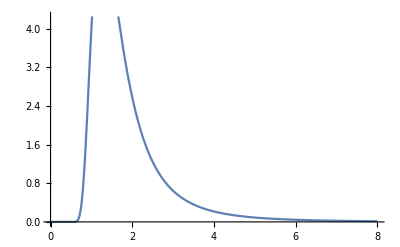

```mathematica
Plot[(4 ⅇ^((8 (-1+x^3))/(3 x^3)))/x^4,{x,0,8}]
```

```mathematica
Manipulate[Plot[(4 ⅇ^((8 (-1+x^3))/(3 x^3 α)))/(x^4 α),{x,-0.014670418244280281,0.014670418244280281}],{α,-0.8167712051709586,0.8167712051709586}]
```

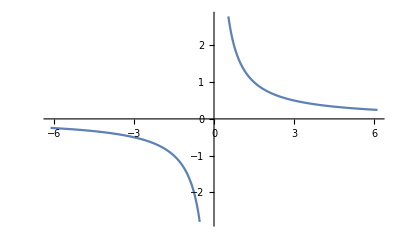

```mathematica
Plot[mt,{x,-6.12,6.12}]
```